# Code

```mathematica
importALPSGenes[filename_]:=Select[Import[filename,"Table"], Length[#] == geneCount&]
```

```mathematica
importALPSOut[filename_] := Select[Import[filename,"Table"], Length[#] == 3&]
```

```mathematica
importGenesFromRun[resultName_, expName_, runNo_] := Module[{file},
file= Last[FileNames[resultName <> "/" <> ToString[expName] <> "/" <> ToString[runNo] <> "-*.pop"]];
importALPSGenes[file]]
```

```mathematica
chartStyle = "DarkRainbow";
```

```mathematica
importResults[directoryName_] := Module[{files},
files = FileNames["output.txt",{directoryName},3];
combineResults[Map[{FileBaseName[DirectoryName[#,2]] , importALPSOut[#]}&, files]]]
```

```mathematica
noChangeColour = Nest[Lighter, Gray,2];
phyloChangeColour = Gray;
ontoChangeColour = Nest[Darker, Gray, 1];
```

```mathematica
boxChartOfResults[res_String] := boxChartOfResults[importResults[res]]
```

```mathematica
boxChartOfResults[res_List] := 
BoxWhiskerChart[values[res], "Median",ChartLegends -> keys[res], ChartStyle -> replicate[{noChangeColour, ontoChangeColour, phyloChangeColour},2] ]
```

```mathematica
chartOfResults[directoryName_String] := chartOfResults[importResults[directoryName]]
```

```mathematica
chartOfResults[res_List] := Module[{},
BarChart[Map[Mean,values[res]], 
	ChartLegends -> keys[res], ChartStyle -> chartStyle]]
```

```mathematica
combineResultsHelper[splitResult_] := Module[{name, justData},
name = splitResult[[1,1]];
justData = Map[#[[2]]&, splitResult];
name ->  Map[#[[-1,-1]]&, justData]]
```

```mathematica
combineResults[results_] := Module[{},
Map[combineResultsHelper, SplitBy[results, #[[1]]&]]]
```

```mathematica
indexOfMinimum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Min[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
indexOfMaximum[fun_, inputs_] := Module[{outputs, min},
outputs = Map[fun, inputs];
min = Max[outputs];
Flatten[Position[outputs, min]]]
```

```mathematica
importMinGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMinimum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importMinGene::notuniq]];
index = First[indexes];
genes[[index]]]
```

```mathematica
importMaxGene[filename_, fitnessForGene_] := Module[{genes, index,  indexes},
genes = importALPSGenes[filename];
indexes = indexOfMaximum[fitnessForGene, genes];
If[Length[indexes] > 1,
Message[importMaxGene::notuniq]];
index = First[indexes];
genes[[index]]]
```

```mathematica
readArray[filename_] := Module[{stream, n, genes},
stream = OpenRead[filename, BinaryFormat -> True];
n  = BinaryRead[stream, "Integer32"];
genes = BinaryReadList[stream, "Real64"];
Close[stream];
genes]
```

# Read Results

```mathematica
<<loadall`
```

```mathematica
loadall[];
```

```mathematica
link = Install["run-simulation-mlink"];
```

```mathematica
Uninstall[link]
```

/Users/shane/School/sussex/thesis/code/src/run-simulation-mlink

```mathematica
Clear[runSimulationMlink]
```

```mathematica
target = {0, 0.1}
```

{0,0.1}

```mathematica
fitness = fitnessToTarge
```

```mathematica
fitness = fitnessToTarget[#, target, Ao, 1]&;
fitnessData = fitnessToTargetData[#, target, Ao, 1]&;
```

```mathematica
fitness = fitnessToTarget[#, target, Ap, 1]&;
fitnessData = fitnessToTargetData[#, target, Ap, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Bp, 1]&;
fitnessData = fitnessForSpeedData[#, Bp, 1]&;
```

```mathematica
fitness = fitnessForSpeed[#, Ap, 1]&;
fitnessData = fitnessForSpeedData[#, Ap, 1]&;
```

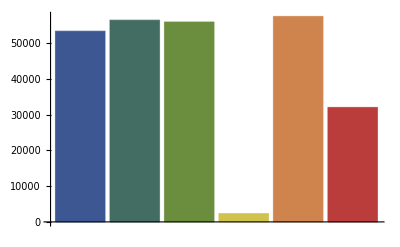
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res9p-target"]
```

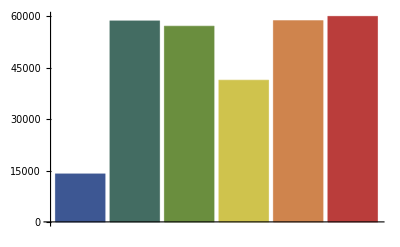
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["res8p-target"]
```

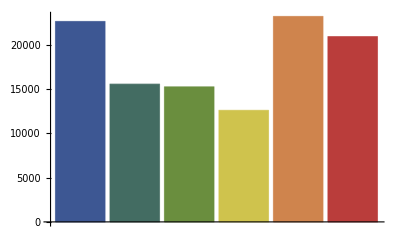
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
chartOfResults["../results/res11p2-target-180"]
```

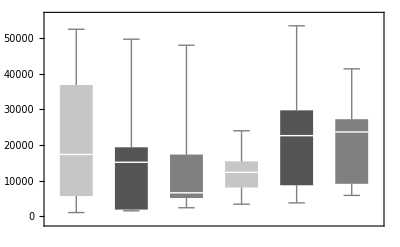
-Graphics--Graphics- | An-t1-l0
-Graphics- | Ao-t1-l0
-Graphics- | Ap-t1-l0
-Graphics- | Bn-t1-l0
-Graphics- | Bo-t1-l0
-Graphics- | Bp-t1-l0

```mathematica
boxChartOfResults["../results/res11p2-target-180"]
```

```mathematica
MannWhitneyTest[{%117[[1]], %117[[3]]}]
```

0.384673

```mathematica
values[%]
```

{{23477,24950,36828,1035,52504,1282,51737,5653,11417,17346},{49714,17484,15319,1523,19363,1870,1868,29880,15158,3325},{6542,5116,48023,2895,16766,2388,36734,10067,17326,6573},{14756,12328,18538,8693,15403,6191,3385,14536,23995,8072},{29143,23658,38837,8694,29737,53476,16298,22633,3754,5657},{27955,23665,24978,8751,26435,41387,27245,5844,9108,13776}}

```mathematica
importResults["res8p-target"]
```

{An-t1-l0→{14000,14000,14000,14000,14000},Ao-t1-l0→{58680,58680,58680,58680,58680},Ap-t1-l0→{57131,57131,57131,57131,57131},Bn-t1-l0→{41363,41363,41363,41363,41363},Bo-t1-l0→{58757,58757,58757,58757,58757},Bp-t1-l0→{59998,59998,59998,59998,59998}}

```mathematica
importResults["res9p-target"]
```

{An-t1-l0→{53339},Ao-t1-l0→{56420},Ap-t1-l0→{55910},Bn-t1-l0→{2326},Bo-t1-l0→{57461},Bp-t1-l0→{32012}}

```mathematica
gene = importMinGene["res9p-target//Bp-t1-l0/r1/pop-phaseFINAL.pop", fitnessToTarget[#, Bp, 4]&]
```

runSimulationMlink::errnan: Saw NaN at time 4.37.

runSimulationMlink::errnan: Saw NaN at time 7.4.

runSimulationMlink::errnan: Saw NaN at time 0.04.

General::stop: Further output of runSimulationMlink :: errnan will be suppressed during this calculation.

{0.81349,0.276377,0.566179,0.00154005,0.381793,1,0.589919,0.203035,0.182151,0.466947,0.571108,0.992006,0.999988,0.760886,0.533334,0.758321,0.922953,0,0.58703,0.718944,0.100702,1,0.0730783,0,0.395888,1,0.853304,0.0650472,0,0,0.565772,0.0870427,0.00397769,0,0.946286,0.952009,0.38389,0.987208,0.603268,0.985946,0.777766,0.327328,0.74215,0.706298,0.40215,0.00367303,0.0631076,0.591608,0.211003,0.216268,0.0102405,0.532021,0.99367,0.995486,0.981314,0.18763,0.349929,0.999899,0.00363319,0.997396,0.175652,0.0567761,0.602251,0.559392,0.218034,0.696494,0.522989,0.174554,0.942035,0.992106,0.00503686,1,0,0.0131671,0.638301,0.860763,0,0.483746,0.122558,0,0.0044752,0.980823,0.995623,0.676887,0.0456941,0.462546,0.256882,0.498715,0.37364,0.160049,0.86087,0.999125,0.496066,0.943525,0.937938,0.421829,0.176201,0.574068,0.228471,1,0.590034,0.0991616,0.00307187,0.957972,0.00579685}

```mathematica
fitnessToTarget[gene, Bp, 4]
```

0.548625

```mathematica
eval[{expName->An,phase->1,tmax->10.000000,evalFailedCount->8,evalSuccCount->22,fitness->0.832979,bestGene->{0.660135,0.732326,0.486698,0.679424,0.661085,0.456736,0.027578,0.015602,0.900535,0.638599,0.632239,0.955804,0.133448,0.707692,0.081565,0.805347,0.809101,0.185128,0.930578,0.154992,0.821429,0.443712,0.399534,0.541282,0.029986,0.459384,0.791260,0.624770,0.875064,0.426925,0.381799,0.174272,0.484513,0.067843,0.919761,0.371030,0.854013,0.547224,0.989620,0.831172,0.176694,0.941317,0.468842,0.555800,0.262177,0.377370,0.369275,0.050764,0.902091,0.584685,0.174256,0.049578,0.587454,0.308074,0.985542,0.241131,0.172690,0.548189,0.289048,0.249246,0.534933,0.861054,0.791295,0.063356,0.576542,0.981148,0.064901,0.949308,0.127447,0.120535,0.141672,0.340873,0.277643,0.403594,0.778580,0.729939,0.279515,0.662023,0.354038,0.159779,0.087506,0.176990,0.658375,0.439769,0.906549,0.179271,0.676231,0.312095,0.649387,0.272254,0.072218,0.188337,0.940468,0.921641,0.994104,0.136249,0.123153,0.347794,0.857751,0.374752,0.731237,0.460226,0.617299,0.935238,0.451753}}]
```

0.885579

```mathematica
eval[{expName->An,phase->1,tmax->10.000000,evalFailedCount->6,evalSuccCount->74,fitness->0.637251,bestGene->{0.184920,0.553883,0.626942,0.954618,0.453786,0.387716,0.228144,0.955603,0.949802,0.735903,0.214667,0.616944,0.762679,0.871502,0.325999,0.072829,0.223703,0.314492,0.828082,0.281538,0.562747,0.306147,0.290256,0.243726,0.023003,0.720173,0.034407,0.800781,0.961513,0.588056,0.454494,0.956262,0.910681,0.022942,0.262506,0.720582,0.143606,0.067164,0.866356,0.417520,0.080647,0.220358,0.459668,0.165166,0.540624,0.284383,0.936643,0.618464,0.793877,0.724930,0.430910,0.157127,0.717570,0.429213,0.061612,0.022604,0.667664,0.459564,0.081057,0.026396,0.095283,0.288617,0.938539,0.466391,0.602577,0.182986,0.390623,0.800897,0.432017,0.265270,0.228479,0.319464,0.153771,0.529591,0.941183,0.932409,0.391586,0.727919,0.935475,0.929828,0.524229,0.605454,0.948668,0.805260,0.558396,0.684106,0.622150,0.342902,0.924218,0.494051,0.345453,0.501936,0.331577,0.700100,0.270487,0.137252,0.552955,0.908109,0.578222,0.850647,0.915199,0.523048,0.479691,0.716950,0.203749}}]
```

0.637192

```mathematica
eval[{expName->Bp,phase->4,tmax->10.000000,evalFailedCount->3,evalSuccCount->49,fitness->0.882153,bestGene->{0.258482,0.220021,0.997129,0.273192,0.150132,0.214955,0.220906,0.984530,0.478883,0.143788,0.189929,0.175679,0.082105,0.776812,0.885521,0.116858,0.782145,0.117549,0.782088,0.928929,0.694345,0.965947,0.947714,0.378324,0.972510,0.954371,0.103804,0.154149,0.926088,0.848946,0.987027,0.890333,0.090770,0.103651,0.078795,0.814093,0.428100,0.725313,0.847334,0.064145,0.878666,0.097427,0.133673,0.806901,0.512209,0.317208,0.000321,0.825203,0.346011,0.795860,0.838634,0.179026,0.677138,0.830643,0.865517,0.981904,0.914906,0.542339,0.422953,0.056406,0.304321,0.390291,0.796151,0.617050,0.202438,0.538656,0.636780,0.793590,0.169122,0.994373,0.787120,0.204689,0.868919,0.932464,0.654913,0.896931,0.827188,0.929365,0.273857,0.107157,0.020221,0.811979,0.026378,0.208938,0.079601,0.950551,0.975824,0.152747,0.181061,0.058430,0.920606,0.031216,0.043508,0.084900,0.011008,0.878814,0.069505,0.823523,0.985121,0.947963,0.179105,0.630945,0.132049,0.899981,0.808470}}]
```

```mathematica
eval[{expName->Ap,phase->4,tmax->10.000000,evalFailedCount->252,evalSuccCount->8360,fitness->0.496894,bestGene->{0.043470,0.000000,0.363149,0.069204,0.408022,1.000000,0.712131,0.354850,0.482484,0.669477,0.583856,0.959850,0.263966,0.486310,0.225465,0.200337,0.000000,0.000000,0.821800,0.852788,0.543651,0.442597,0.134739,0.415681,0.880949,0.347316,0.548337,0.498873,0.223762,0.859324,0.348699,0.620226,0.624340,0.479589,0.010222,0.909806,0.726839,0.698118,0.189367,0.000000,1.000000,0.532150,0.000000,0.535506,0.418991,0.857100,1.000000,0.346641,0.002683,0.603374,0.566655,0.525998,0.355919,0.990284,0.196503,0.960747,0.265764,1.000000,0.614048,0.357417,0.992313,0.999250,0.009813,1.000000,1.000000,0.309098,1.000000,1.000000,0.674354,0.296608,0.943379,0.298063,0.755494,0.063434,0.629850,0.000000,1.000000,1.000000,0.325854,0.379243,0.317250,0.536041,0.305432,0.793253,0.817857,0.591388,0.883433,0.843244,0.818056,0.851799,0.528285,0.000000,0.000000,0.480621,0.773957,0.463891,0.782318,0.666030,0.648062,0.001099,0.597034,0.000000,0.138971,0.000000,0.700075}}]
```

runSimulationMlink::errnan: Saw NaN at time 4.56.

666.6

```mathematica
eval[{expName->Ap,phase->1,tmax->10.000000,evalFailedCount->1,evalSuccCount->247,fitness->0.487540,bestGene->{0.646719,0.308916,0.550125,0.545020,0.579394,0.119550,0.663899,0.703834,0.299207,0.253744,0.205792,0.693521,0.203383,0.474145,0.162049,0.515473,0.563819,0.837867,0.687400,0.935854,0.651325,0.491819,0.430778,0.697017,0.279920,0.467867,0.516793,0.321004,0.349146,0.297971,0.712387,0.257341,0.400917,0.167257,0.425541,0.647007,0.735800,0.409622,0.596076,0.439953,0.429047,0.579146,0.498287,0.510336,0.693394,0.540861,0.124406,0.222264,0.748822,0.528991,0.732882,0.254625,0.317099,0.481864,0.500638,0.724945,0.072407,0.396321,0.637897,0.388801,0.425131,0.789925,0.524317,0.640757,0.534669,0.338609,0.508871,0.409988,0.432051,0.914406,0.611563,0.678465,0.486552,0.593565,0.378905,0.592295,0.513294,0.568241,0.344186,0.556796,0.928474,0.386144,0.503380,0.423308,0.749024,0.471442,0.753352,0.874622,0.261425,0.117730,0.565289,0.111563,0.760872,0.469622,0.487906,0.488203,0.176879,0.573179,0.172407,0.156733,0.549323,0.522392,0.573291,0.332482,0.157415}}]
```

1.04989

```mathematica
eval[{expName->Ap,phase->3,tmax->10.000000,evalFailedCount->1,evalSuccCount->8048,fitness->0.499627,bestGene->{0.069562,0.000000,0.368224,0.091715,0.402287,1.000000,0.681739,0.379752,0.462472,0.670506,0.582690,0.935751,0.274626,0.502564,0.262240,0.226714,0.000000,0.000000,0.800487,0.852254,0.540599,0.469022,0.175646,0.430000,0.841017,0.374055,0.524910,0.486418,0.216334,0.862400,0.367020,0.597325,0.602058,0.467161,0.000000,0.879402,0.709541,0.675763,0.189501,0.000000,1.000000,0.533839,0.000000,0.544690,0.407462,0.832442,1.000000,0.331454,0.000000,0.582309,0.568611,0.509074,0.345688,0.984452,0.200312,0.937122,0.287086,1.000000,0.602768,0.355171,0.987699,1.000000,0.015703,1.000000,1.000000,0.333331,1.000000,1.000000,0.665626,0.287145,0.922356,0.302793,0.754529,0.069284,0.643420,0.000000,1.000000,1.000000,0.312261,0.385860,0.342437,0.546971,0.312874,0.787771,0.793050,0.605294,0.843889,0.814133,0.818546,0.813735,0.524706,0.000000,0.000000,0.492041,0.769510,0.454087,0.780959,0.651127,0.656642,0.000000,0.576069,0.000000,0.175308,0.000000,0.683716}}]
```

0.920209

```mathematica
data  = evalData[{expName->Ap,phase->4,tmax->10.000000,evalFailedCount->252,evalSuccCount->8360,fitness->0.496894,bestGene-> readArray["pop-phase4-genes.bin"]}]
```

runSimulationMlink::errnan: Saw NaN at time 9.95.

```mathematica
eval[{expName->Bp,phase->4,tmax->10.000000,evalFailedCount->0,evalSuccCount->67,fitness->0.872027,bestGene->{0.102740,0.060705,0.418557,0.945856,0.551595,0.332889,0.103278,0.962664,0.071786,0.987224,0.110931,0.349346,0.844304,0.119783,0.476552,0.661479,0.446698,0.937061,0.516714,0.995462,0.224034,0.642197,0.935954,0.140566,0.098248,0.376135,0.027201,0.707535,0.559623,0.651314,0.089626,0.422169,0.496530,0.991605,0.846448,0.832511,0.114056,0.446093,0.843690,0.118213,0.696153,0.952299,0.839594,0.760462,0.758870,0.331449,0.423898,0.342334,0.101663,0.874083,0.472561,0.237661,0.087397,0.189760,0.679281,0.813028,0.939030,0.337279,0.072423,0.148474,0.344773,0.243836,0.834984,0.311308,0.521030,0.407878,0.828341,0.144361,0.343101,0.816485,0.906617,0.504473,0.786966,0.306978,0.051894,0.474837,0.030274,0.328487,0.612890,0.672201,0.845570,0.645939,0.469744,0.349923,0.585016,0.322611,0.173129,0.295110,0.564113,0.307401,0.595355,0.883265,0.561123,0.555515,0.515154,0.192710,0.141025,0.193713,0.739266,0.110981,0.786135,0.793047,0.698578,0.537685,0.781420}}]
```

0.947584

```mathematica
Close["genes.bin"]
```

genes.bin

```mathematica
readArray["genes.bin"]
```

{1.,0.870639,0.940525,0.,0.,0.,0.,0.452882,1.,0.328426,0.,0.935167,1.,0.669668,1.,0.0154214,1.,1.,0.763599,0.00330799,0.0628294,0.356791,0.,0.595901,0.24031,0.708497,1.,0.,1.,0.893923,1.,0.990931,0.886191,0.,1.,0.636767,0.,0.732724,0.,0.404838,0.,0.938284,0.108883,0.273805,1.,0.764809,0.,0.,0.,0.,0.416928,0.413397,0.935507,0.,1.,1.,0.,1.,0.239237,0.513079,1.,0.,1.,0.595014,0.167292,0.,1.,0.090893,0.,0.606157,0.,0.975624,1.,0.246117,0.,0.,1.,0.,1.,0.589887,1.,0.128627,0.749559,0.355478,1.,0.,0.,0.,0.733698,0.926027,1.,0.148651,1.,1.,0.0532964,1.,0.434692,0.511501,1.,1.,0.,0.,1.,0.,0.}

```mathematica
myGenes = %;
```

```mathematica
eval[{bestGene -> myGenes, expName->Bp,phase->4,tmax->10.000000,evalFailedCount->0,evalSuccCount->31,fitness->0.781333,bestGene->{1.000000,0.870639,0.940525,0.000000,0.000000,0.000000,0.000000,0.452882,1.000000,0.328426,0.000000,0.935167,1.000000,0.669668,1.000000,0.015421,1.000000,1.000000,0.763599,0.003308,0.062829,0.356791,0.000000,0.595901,0.240310,0.708497,1.000000,0.000000,1.000000,0.893923,1.000000,0.990931,0.886191,0.000000,1.000000,0.636767,0.000000,0.732724,0.000000,0.404838,0.000000,0.938284,0.108883,0.273805,1.000000,0.764809,0.000000,0.000000,0.000000,0.000000,0.416928,0.413397,0.935507,0.000000,1.000000,1.000000,0.000000,1.000000,0.239237,0.513079,1.000000,0.000000,1.000000,0.595014,0.167292,0.000000,1.000000,0.090893,0.000000,0.606157,0.000000,0.975624,1.000000,0.246117,0.000000,0.000000,1.000000,0.000000,1.000000,0.589887,1.000000,0.128627,0.749559,0.355478,1.000000,0.000000,0.000000,0.000000,0.733698,0.926027,1.000000,0.148651,1.000000,1.000000,0.053296,1.000000,0.434692,0.511501,1.000000,1.000000,0.000000,0.000000,1.000000,0.000000,0.000000}}]
```

0.781333